Relations

## Introduction

In this chapter, we will learn how to use Mathematica to work with relations. We explain how to represent binary relations using sets of ordered pairs, zero–one matrices, and directed graphs. We show how to use Mathematica to determine whether a relation has various properties using these different representations.

We also describe how to compute closures of relations. In particular, we show how to find the transitive closure of a relation using two different algorithms and we compare the time performance of these algorithms. After explaining how to use Mathematica to work with equivalence relations, we show how to use Mathematica to work with partial orderings, to draw Hasse diagrams, and to implement topological sorting.

Some readers may be familiar with the Combinatorica package. While this package has much to offer, many of the functions it was created to provide are now part of the Wolfram Language proper. In this manual, we tend to avoid use of the Combinatorica package functions, particularly when there are Wolfram Language functions that will suffice.

## 9.1 Relations and Their Properties

The first step in understanding and manipulating relations in Mathematica is to determine how to represent them. There are no specific functions in the Wolfram Language designed to handle relations. We will implement relations using the most convenient form for the question at hand. In this chapter, we will make use of sets of ordered pairs, zero–one matrices, and directed graphs in order to explore relations in Mathematica.

### Relations as Ordered Pairs

First, we will represent relations as lists of ordered pairs. We begin by defining a predicate to check that an expression is a relation, that is, a list of pairs. Our reason for defining a predicate is that it gives us a way to ensure that when arguments are passed to functions we write, the arguments are valid for that function. As an illustration of the utility of this approach, consider the function below.

```mathematica
posIntQ[n_]:=IntegerQ[n]&&n>0
```

```mathematica
myFactorial[n_?posIntQ]:=Module[{},
If[n==1,
Return[1],
Return[n*myFactorial[n-1]]
]
]
```

In this simple example, we define a predicate posIntQ that tests input for being both an integer and positive. Then, the function myFactorial uses the PatternTest (?) structure to declare that the function’s definition is only valid for those inputs that satisfy the requirements of the posIntQ predicate. Consider the result of attempting to compute the factorial of -3:

```mathematica
myFactorial[-3]
```

myFactorial[-3]

The function does not try to execute, but simply echoes the input, indicating that the function was not able to operate on that input. It is usually better for a function to not try to compute on invalid input. In the case of myFactorial, omitting the predicate would result in an infinite recursion.

We could also deal with the problem of potentially invalid arguments by checking the arguments within the body of the function. The PatternTest (?) approach, however, makes the requirements for the arguments much clearer and also serves to keep the actual work of the function separate from input validation.

As mentioned, we are going to first represent relations as lists of ordered pairs. We will define two predicates. First, an ordered pair predicate that we call pairQ. Second, the relation type, which will be called relationQ, will be defined to be a list of pairs. We define the pair predicate as follows:

```mathematica
pairQ[{_,_}]:=True;
pairQ[___]:=False
```

The first line of the definition says what a pair is. If pairQ is passed an argument that is a list containing two elements, then it returns True. Those elements can be anything at all, including lists and other structures, which allows us to define relations among complex structures. The second line of the definition says that if pairQ is passed any argument at all, or no argument, it should produce False. The BlankNullSequence (___), formed from three underscores, matches any expression, comma-separated sequence of expressions, or no expression at all. This is different from BlankSequence (__), two underscores, which cannot match an empty argument.

You might think that the second definition overwrites the first, since it is more general. In fact, in the Wolfram Language, both definitions remain valid. When applied to input, the more specific definition is attempted first, and the first definition that can match the input is applied. Thus, if you give pairQ an argument that is in fact a pair, the argument will match the pattern of the first definition and return True.

```mathematica
pairQ[{5,"b"}]
```

True

However, for any argument that does not match that pattern, Mathematica will go to the second definition, which matches anything, and output False.

```mathematica
pairQ[5]
```

False

```mathematica
pairQ[{5,6,7}]
```

False

```mathematica
pairQ[2,3]
```

False

```mathematica
pairQ[]
```

False

With pairQ in place, we define relationQ.

```mathematica
relationQ[{___?pairQ}]:=True;
relationQ[___]:=False
```

In this case, the first line insists that a relation must be a list containing a BlankNullSequence (___), that is, a comma-separated sequence of expressions, each one of which satisfies pairQ. In other words, a (binary) relation is a set of ordered pairs.

### Creating Relations

Now that we have established the relation predicate, we will create an actual relation.

#### The Divides Relation

Example 4 in Section 9.1 describes the “divides relation,” that is, R={(a,b)|a divides b}. We will write a function to construct this relation. The function will consider every possible ordered pair of elements and will include them in the relation if they satisfy the condition that b is divisible by a, using the Divisible function.

We use the Tuples function to generate all possible pairs of a list of elements. It takes two arguments: the list of elements is the first argument, and 2 will be the second argument to indicate that we desire pairs of elements. For example, the following creates all pairs of elements from {1,2,3}.

```mathematica
Tuples[{1,2,3},2]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

To the output of Tuples, we apply Select to obtain the sublist of elements that satisfy the divisibility condition. Select requires two arguments. The first is the list of elements to select from. The second is a function name or a pure Function (&) that returns True for the desired elements. We will use a pure Function (&) to apply the Divisible function to the arguments in reverse order.

The dividesRelation function below uses these ideas. Its argument is a list of integers, and it produces the relation.

```mathematica
dividesRelation[A:{__Integer}]:=Select[Tuples[A,2],Divisible[#[[2]],#[[1]]]&]
```

We use the function to construct the divides relation on the integers 1 through 4.

```mathematica
dividesRelation[Range[4]]
```

{{1,1},{1,2},{1,3},{1,4},{2,2},{2,4},{3,3},{4,4}}

We can check that this function has produced an expression that satisfies relationQ.

```mathematica
relationQ[%]
```

True

For convenience, we can overload the dividesRelation symbol to also accept a single positive integer n as the argument and construct the “divides relation” on {1,2,…,n}.

```mathematica
dividesRelation[n_Integer]:=Select[Tuples[Range[n],2],Divisible[#[[2]],#[[1]]]&]
```

For example:

```mathematica
div6=dividesRelation[6]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{2,2},{2,4},{2,6},{3,3},{3,6},{4,4},{5,5},{6,6}}

#### The Inverse of a Relation

Now that we have seen an example of a function that creates a relation, we look at a simple example of a function that manipulates a relation.

For any relation R, its inverse relation, denoted R^-1 is defined by R^-1={(b,a)|(a,b)∈R}. The following function computes the inverse of a relation.

```mathematica
inverseRelation[R_?relationQ]:=Reverse[R,2]
```

The Reverse function is used to reverse the elements of a list. Given a list as a sole argument, Reverse simply inverts the order.

```mathematica
Reverse[{1,2,3}]
```

{3,2,1}

Reverse accepts a second optional argument to specify a level. In this case, we use 2 to indicate that we want Reverse to change the order of the sublists of the relation, not the order of the elements of R itself.

Since we have defined the “divides” relation, we can use the inverseRelation function to create the “multiple of” relation.

```mathematica
mul6=inverseRelation[div6]
```

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{2,2},{4,2},{6,2},{3,3},{6,3},{4,4},{5,5},{6,6}}

### Properties of Relations

Mathematica can be used to determine if a relation on a set has a particular property, such as reflexivity, symmetry, antisymmetry, or transitivity. This can be accomplished by creating functions with the Wolfram Language that take as input the given relation, examine the elements of the relation, and return True or False based on whether the relation has the property or not.

Before writing functions to test for properties of relations, it will be convenient to have a routine that extracts the domain of a given relation on a set. This function works by applying Flatten to the relation. Note that it may be the case that the objects in our relation are themselves lists, for example, the subset relation. For this reason, we give Flatten the second argument 1, indicating that it should only flatten the list down to the first level. This way, if the pairs in the relation are elements, the pairs will be preserved, as shown below.

```mathematica
subsets2={{{},{1}},{{},{2}},{{},{1,2}},{{1},{1,2}},{{2},{1,2}},{{1,2},{1,2}}};
```

```mathematica
Flatten[subsets2,1]
```

{{},{1},{},{2},{},{1,2},{1},{1,2},{2},{1,2},{1,2},{1,2}}

After flattening, we apply Union to remove duplicates and put the output in canonical order.

Note that, strictly speaking, the result from this function need not equal the domain of the relation, since there may exist elements in the domain that are not related to any object in the domain. It might be better to call this the “effective domain” of the relation. Also note that this function presumes that the relation is a relation on a set, as distinguished from a relation from one set to a different set.

```mathematica
findDomain[R_?relationQ]:=Union[Flatten[R,1]]
```

Observe that this gives the expected output for both the “divides” relation and the subsets relation.

```mathematica
findDomain[div6]
```

{1,2,3,4,5,6}

```mathematica
findDomain[subsets2]
```

{{},{1},{2},{1,2}}

#### Reflexivity

We are now ready to begin testing relations for various properties. The first property we consider is reflexivity. Remember that a relation R is reflexive if (a,a)∈R for every a in the domain.

To check to see if a relation is reflexive, we compute the domain of the relation and then check each element a of the domain to see if (a,a) is in the relation. If the function finds an element of the domain with (a,a)∉R, then it throws False immediately. If the function checks all of the members of the domain with no failures, then it evaluates to True.

```mathematica
reflexiveQ[R_?relationQ]:=Module[{a,domain},
domain=findDomain[R];
Catch[
Do[If[!MemberQ[R,{a,a}],Throw[False]]
,{a,domain}];
Throw[True]
]
]
```

Recall that the Do function’s second argument, {a,domain} specifies that the variable a is to be assigned to every member of the list domain. Also recall that MemberQ expects its first argument to be the list and the second argument to be the element being sought.

We can use this on the “divides” relation.

```mathematica
reflexiveQ[div6]
```

True

#### Symmetry

Next, we will examine the symmetric and antisymmetric properties. To determine whether a relation is symmetric, we simply use the definition. That is, we check, for every member (a,b)∈R, whether (b,a) is also a member of the relation. If we discover a pair in the relation for which the reverse pair is not in the relation, then we know that the relation is not symmetric. Otherwise, it must be symmetric. This is the logic employed by the following function.

```mathematica
symmetricQ[R_?relationQ]:=Module[{u},
Catch[
Do[If[!MemberQ[R,Reverse[u]],Throw[False]]
,{u,R}];
Throw[True]
]
]
```

For example, we can see that the “divides” relation is not symmetric.

```mathematica
symmetricQ[div6]
```

False

The union of “divides” and “multiple of” is symmetric, however.

```mathematica
divOrMul6=Union[div6,mul6]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{2,1},{2,2},{2,4},{2,6},{3,1},{3,3},{3,6},{4,1},{4,2},{4,4},{5,1},{5,5},{6,1},{6,2},{6,3},{6,6}}

```mathematica
symmetricQ[divOrMul6]
```

True

To determine whether a given relation R is antisymmetric, we again use the definition. Remember that a relation is antisymmetric when it has the property that whenever a pair (a,b) and its reverse (b,a) both belong to R, then it must be that a=b. To check this, we simply loop over all members u of R and see if the opposite pair belongs to R and whether the members of the pair are different.

```mathematica
antisymmetricQ[R_?relationQ]:=Module[{u},
Catch[
Do[If[u[[1]]≠u[[2]]&&MemberQ[R,Reverse[u]],Throw[False]]
,{u,R}];
Throw[True]
]
]
```

We now use this function to check if the “divides” and “multiple of” relations defined earlier are antisymmetric.

```mathematica
antisymmetricQ[div6]
```

True

```mathematica
antisymmetricQ[mul6]
```

True

#### Transitivity

The transitive property is the most difficult to check. Recall the definition of transitive relations: a relation R is transitive if, whenever (a,b) and (b,c) are in R, then (a,c) must be as well.

To check transitivity, we will consider all possible a, b, and c in the domain of R. Then, if (a,b)∈R, (b,c)∈R, and (a,c)∉R, we know that the relation is not transitive. If there is no such triple a,b,c to contradict transitivity, then we conclude that the relation is transitive.

Here is the function.

```mathematica
transitiveQ[R_?relationQ]:=Module[{domain,a,b,c},
domain=findDomain[R];
Catch[
Do[If[MemberQ[R,{a,b}]&&MemberQ[R,{b,c}]&&!MemberQ[R,{a,c}],Throw[False]]
,{a,domain},{b,domain},{c,domain}];
Throw[True]
]
]
```

We see that the “divisible” relation is transitive. However, we can modify it to fail to be transitive by removing the (1,6) pair, since (1,2) and (2,6) are in R.

```mathematica
transitiveQ[div6]
```

True

```mathematica
r2=Complement[div6,{{1,6}}]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{2,2},{2,4},{2,6},{3,3},{3,6},{4,4},{5,5},{6,6}}

```mathematica
transitiveQ[r2]
```

False

## 9.2 n-ary Relations and Their Applications

Using Mathematica, we can construct an n-ary relation where n is a positive integer. As in the previous section, we will begin by defining predicates both for the elements of the relation (tupleQ) and for the n-ary relation (nrelationQ). The only difference here, as compared to the predicates we defined in the previous section, is that we do not know the length of the list that makes up a tuple.

```mathematica
tupleQ[_List]:=True;
tupleQ[___]:=False
```

```mathematica
nrelationQ[{__?tupleQ}]:=True;
nrelationQ[___]:=False
```

Consider the following 4-ary relation that represents student records.

```mathematica
r3={{"Adams",9012345,"Politics",2.98},{"Woo",9100055,"Film Studies",4.99},{"Warshall",9354321,"Mathematics",3.66}};
```

The first field represents the name of the student, the second field is the student ID number, the third field is the students’ home department, and the last field stores the student’s grade point average. Note that this relation satisfies nrelationQ.

```mathematica
nrelationQ[r3]
```

True

While we created a very generic n-ary relation predicate, you can also create more specific predicates for particular situations. For instance, the tuples in the relation above will always consist of a string, integer, string, and a floating point number. We make the following predicate specifically for that kind of relation.

```mathematica
studentRecordQ[{_String,_Integer,_String,_Real}]:=True;
studentRecordQ[___]:=False
```

```mathematica
studentRelationQ[{__?studentRecordQ}]:=True;
studentRelationQ[___]:=False
```

```mathematica
studentRelationQ[r3]
```

True

### Operations on n-ary Relations

Now, we will create functions that act on n-ary relations to compute projections and the join of relations.

#### Projection

We will construct a function for computing a projection of a relation. The function takes as input an expression satisfying nrelationQ along with a list of integers representing the indices of the fields that are to remain. The output will be another n-ary relation.

```mathematica
projectRelation[R_?nrelationQ,P:{__Integer}]:=R[[All,P]]
```

The expression R[[All,P]] returns the list formed by taking every element of R and extracting the sublists defined by the indices in the list P.

We can use this function with the relation we created earlier.

```mathematica
projectRelation[r3,{2,4}]
```

{{9012345,2.98},{9100055,4.99},{9354321,3.66}}

```mathematica
projectRelation[r3,{3,4,1}]
```

{{Politics,2.98,Adams},{Film Studies,4.99,Woo},{Mathematics,3.66,Warshall}}

#### Join

Now, consider joins of relations, as defined in the textbook in Section 9.2. The join operation has applications to databases when tables of information need to be combined in a meaningful manner.

The join function that we will implement here follows the following outline:

Input two relations R and S and a positive integer p, representing the overlap between the relations.

Examine each element u of R and determine the last p fields of u.

Examine all elements v of S to determine if the first p fields of v match the last p fields of u.

Upon finding a match, we combine the elements and place the result in a relation T, which is returned as the output of the function.

```mathematica
joinRelation[R_?nrelationQ,S_?nrelationQ,p_Integer]:=Module[{overlapR,i,u,v,x,joinElement,T={}},
Do[
x=u[[-p;;-1]];
Do[
If[v[[1;;p]]==x,
joinElement=Join[u,v[[p+1;;-1]]];
AppendTo[T,joinElement]
]
,{v,S}]
,{u,R}];
T
]
```

The joinRelation function beings by initializing the return relation, T, to the empty list. The outer Do loop assigns the variable u to each tuple in the relation R. It immediately assigns x to the last p elements of u. This is the portion that is supposed to overlap with elements from the other relation. Note the use of the Span (;;) operator. The span -p;;-1 in the Part ([[…]]) applied to u refers to the span from -p to -1, that is, from the element p from the end of the list u to the last element of u.

The inner Do loop assigns the variable v to each tuple in the relation S. The body of the loop is an If statement that checks whether the first p elements of v agree with the last p elements of u (stored in x). If that holds, that is, the two elements overlap, then joinElement is created by applying the Wolfram Language Join function to u and the rest of v. This new object is then added to the relation T, which is the output of the function.

We apply the joinRelation function to Example 11 of Section 9.2.

```mathematica
teachingAssignments={
{"Cruz","Zoology",335},
{"Cruz","Zoology",412},
{"Farber","Psychology",501},
{"Farber","Psychology",617},
{"Grammer","Physics",544},
{"Grammer","Physics",551},
{"Rosen","Computer Science",518},
{"Rosen","Mathematics",575}};
```

```mathematica
classSchedule={
{"Computer Science",518,"N521","2:00 P.M."},
{"Mathematics",575,"N502","3:00 P.M."},
{"Mathematics",611,"N521","4:00 P.M."},
{"Physics",544,"B505","4:00 P.M."},
{"Psychology",501,"A100","3:00 P.M."},
{"Psychology",617,"A110","11:00 A.M."},
{"Zoology",335,"A100","9:00 A.M."},
{"Zoology",412,"A100","8:00 A.M."}};
```

We apply joinRelation and use TableForm to make the output readable.

```mathematica
joinRelation[teachingAssignments,classSchedule,2]//TableForm
```

Cruz | Zoology | 335 | A100 | 9:00 A.M.
Cruz | Zoology | 412 | A100 | 8:00 A.M.
Farber | Psychology | 501 | A100 | 3:00 P.M.
Farber | Psychology | 617 | A110 | 11:00 A.M.
Grammer | Physics | 544 | B505 | 4:00 P.M.
Rosen | Computer Science | 518 | N521 | 2:00 P.M.
Rosen | Mathematics | 575 | N502 | 3:00 P.M.

### Datasets

The discussion above illustrates how one could implement n-ary relations using lists, one of the most basic data structures. However, with databases specifically in mind, the Wolfram Language Dataset structure is much more powerful. On the surface, a Dataset consists of nested List and Association objects. But wrapping those more basic structures inside a Dataset provides access to sophisticated queries and operations.

We first described the Association structure in Section 2.2 of this manual in reference to fuzzy sets. In other languages, associations may be referred to as dictionaries, maps, or hash tables. An Association is comprised of a collection of key–value pairs, with the keys being unique. You can enter an Association as a list of Rule (->) elements within the Association head or between the delimiters <| and |>. Be aware that the word association is used very differently in the textbook than it is in the Wolfram Language. Here, the word association will be used exclusively to refer to the data structure.

Using the teaching assignments example from the text, we would implement each row of the table as an association, with the field names as the keys and the data in the row as the values. For example, Ken Rosen’s mathematics teaching assignment would be represented by the association shown below.

```mathematica
rosenmathclass=<|"Professor"->"Rosen","Department"->"Mathematics","Course_number"->575|>
```

<|Professor→Rosen,Department→Mathematics,Course_number→575|>

Note that we have entered the values as strings and integers, which is appropriate to the kind of data being stored in those fields. We also used strings for the keys. While it is tempting, and allowed, to forgo typing the quotation marks and using symbols for the keys instead, there are some benefits to using strings as the keys in an Association.

Accessing the value corresponding to a specific key is done using function notation.

```mathematica
rosenmathclass["Course_number"]
```

575

Combining this notation with Set (=) can be used to change values, or even add keys.

The functions Keys and Values applied to an Association will produce a list of the keys and values.

```mathematica
Keys[rosenmathclass]
```

{Professor,Department,Course_number}

```mathematica
Values[rosenmathclass]
```

{Rosen,Mathematics,575}

Rather than type all of the rows in the teaching assignment database, we will make use of the teachingAssignments list of lists above. The AssociationThread function is designed to take a list of keys and a list of values and form the association in which each key is paired with the value in the corresponding position. For example, we can transform the first row of teachingAssignments into an Association with the code below.

```mathematica
AssociationThread[{"Professor","Department","Course_number"},teachingAssignments[[1]]]
```

<|Professor→Cruz,Department→Zoology,Course_number→335|>

Thus, we can form the list of associations corresponding to the teaching assignments table by applying Table over all the elements of teachingAssignments.

```mathematica
Table[AssociationThread[{"Professor","Department","Course_number"},row],{row,teachingAssignments}]
```

{<|Professor→Cruz,Department→Zoology,Course_number→335|>,<|Professor→Cruz,Department→Zoology,Course_number→412|>,<|Professor→Farber,Department→Psychology,Course_number→501|>,<|Professor→Farber,Department→Psychology,Course_number→617|>,<|Professor→Grammer,Department→Physics,Course_number→544|>,<|Professor→Grammer,Department→Physics,Course_number→551|>,<|Professor→Rosen,Department→Computer Science,Course_number→518|>,<|Professor→Rosen,Department→Mathematics,Course_number→575|>}

This is exactly the input required to create a Dataset with named columns.

```mathematica
teachingAssignmentDB=Dataset[Table[AssociationThread[{"Professor","Department","Course_number"},row],{row,teachingAssignments}]]
```

Dataset[<>]

To recover the list of associations from a Dataset, apply the Normal function.

```mathematica
Normal[teachingAssignmentDB]
```

{<|Professor→Cruz,Department→Zoology,Course_number→335|>,<|Professor→Cruz,Department→Zoology,Course_number→412|>,<|Professor→Farber,Department→Psychology,Course_number→501|>,<|Professor→Farber,Department→Psychology,Course_number→617|>,<|Professor→Grammer,Department→Physics,Course_number→544|>,<|Professor→Grammer,Department→Physics,Course_number→551|>,<|Professor→Rosen,Department→Computer Science,Course_number→518|>,<|Professor→Rosen,Department→Mathematics,Course_number→575|>}

With a Dataset, we can access parts of the database using the Part ([[…]]) operator. Keep in mind that the underlying structure is a list of associations. So we can access the third row by

```mathematica
teachingAssignmentDB[[3]]
```

Dataset[<>]

However, one of the benefits of the Dataset is that the Part ([[…]]) operator is extended by the query syntax ([…]). All of the usual syntax you would normally use with Part ([[…]]) can be used in single brackets with a Dataset.

```mathematica
teachingAssignmentDB[3]
```

Dataset[<>]

To access the department of the teaching assignment in the third row, we enter

```mathematica
teachingAssignmentDB[3,"Department"]
```

Psychology

We can use lists and ranges to extract different pieces of the database, just as we have done with lists. The code below accesses the department and course number for the second through fourth rows of the database.

```mathematica
teachingAssignmentDB[2;;4,{"Department","Course_number"}]
```

Dataset[<>]

The symbol All can be used as well.

```mathematica
teachingAssignmentDB[All,{"Department","Course_number"}]
```

Dataset[<>]

Note that the above is the projection operation.

We create a Dataset for the class schedule table in the same way.

```mathematica
classScheduleDB=Dataset[Table[AssociationThread[{"Department","Course_number","Room","Time"},row],{row,classSchedule}]]
```

Dataset[<>]

The query syntax, though, is much more flexible than the Part ([[…]]) operator. Suppose, for example, we wish to extract all of the courses held in room A100. If we were dealing with a list, we use use the Select function. With a Dataset, we use Select in conjunction with the query syntax.

The argument to Select will be a function, in this case, a pure function that applies to an Association and returns true or false. When defining a pure function that operates on an Association, there is a special Slot (#) syntax. Provided that the key has been defined as a string, the value associated to the key “key” can be referenced by #key.

To select the classes in room A100, we just need to define the function that tests whether #Room equals “A100”. Remember to terminate the Function definition with an ampersand.

```mathematica
classScheduleDB[Select[#Room=="A100"&]]
```

Dataset[<>]

When the key is more complicated, it may be necessary to include quotation marks; the following selects the courses with numbers greater than 500. Without the quotation marks, it would raise an error.

```mathematica
classScheduleDB[Select[#"Course_number">500&]]
```

Dataset[<>]

The Wolfram Language provides a more flexible version of join, called JoinAcross, than is described in the textbook. In particular, there is no requirement that the matching columns be at the end and beginning of the two databases. Rather, the keys are used to determine which values need to agree in order for two rows to be joined.

The JoinAcross function requires three arguments. The first two are Dataset objects or lists of associations. The third argument is a key or list of keys which specify which fields must agree for two database entries to be combined. As in Example 11 of the textbook, we will combine the teaching assignment and class schedule databases by joining rows which have matching department and course number.

```mathematica
JoinAcross[teachingAssignmentDB,classScheduleDB,{"Department","Course_number"}]
```

Dataset[<>]

Observe that, as with the solution to the example in the text, entries in one table without a corresponding entry in the other do not appear in the joined Dataset. This is the default behavior, but there are other options. Adding “Outer” as a fourth argument will produce a Dataset that includes all the data of both of the original two databases.

```mathematica
JoinAcross[teachingAssignmentDB,classScheduleDB,{"Department","Course_number"},"Outer"]
```

Dataset[<>]

Other options are “Left” and “Right”, which ensure that all of the data in the respective argument are included, and “Inner”, which is the default.

## 9.3 Representing Relations

From this point forward, we will consider binary relations exclusively. This gives us additional options for how we represent relations. In this section, we will see how to represent binary relations with zero–one matrices and digraphs.

### Representing Relations Using Matrices

We begin with representations of relations with zero–one matrices.

#### A First Example

We create a matrix as a list of lists, where the inner lists store the elements in the rows of the matrix. The MatrixForm function will display the matrix in the usual form.

```mathematica
{{1,2},{3,4}}//MatrixForm
```

(1 | 2
3 | 4)

Be careful to not use MatrixForm in conjunction with an assignment, lest the MatrixForm be permanently attached to the matrix, which can cause other functions to fail.

When working with matrix representations of relations, it can be useful to begin with a matrix of the correct size filled entirely with 0s, and then modify that matrix as needed. To do this, you can use the ConstantArray function. The first argument to ConstantArray is the constant that will be used as the filler in the resulting list. The second argument specifies the dimension. For an ordinary list, the second argument is the length of the list. For a matrix, the second argument must be a pair specifying the number of rows and the number of columns.

For example, to create a 4×4 matrix filled with 0s, you would enter the following expression.

```mathematica
exampleMatrix=ConstantArray[0,{4,4}];
exampleMatrix//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Right now, this matrix does not represent a very interesting relation. We need to change entries to 1 to represent elements of the domain that are related to each other. For instance, if (1,2)∈R then we need to change the (1,2) entry to a 1. To do this, we use Part ([[…]]) and Set (=) to specify the location and make the assignment.

```mathematica
exampleMatrix[[1,2]]=1
```

1

We can see that it modified the matrix.

```mathematica
exampleMatrix//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

We make this matrix represent the relation “is one less than” on {1,2,3,4}, as in, “1 is one less than 2.”

```mathematica
exampleMatrix[[2,3]]=1;
exampleMatrix[[3,4]]=1;
exampleMatrix//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

#### Transforming a Set of Pairs Representation into a Matrix Representation

Now, we create a function to turn a relation satisfying relationQ (defined in Section 9.1 of this manual) into a matrix representation. Doing so is fairly straightforward. Given a relation R, whose domain consists of integers, we can use findDomain from above to extract the domain. We then create a square matrix whose size is equal to the largest integer in the domain, which we can obtain with the Max function. Then, we simply loop through the elements of the relation and set the value of the corresponding entry in the matrix to 1.

```mathematica
relationToMatrix[R_?relationQ]:=Module[{u,max,m},
max=Max[findDomain[R]];
m=ConstantArray[0,{max,max}];
Do[m=ReplacePart[m,u->1]
,{u,R}];
m
]
```

Note the use of ReplacePart to modify the matrix m. Recall that elements of the relation R are pairs, such as {1,2}. The expression m[[u]]=1, therefore, would be resolved to an expression of the form m[[{1,2}]]=1. This does not set the (1,2) element of m to 1, however. Rather, m[[{1,2}]] represents the list consisting of the first and second elements of m, that is, m[[{1,2}]] is the first two rows of m. ReplacePart allows us to use the pair {1,2} to reference the (1,2) entry of m. The ReplacePart function’s first argument is an expression to be manipulated, such as the matrix m. Its second argument is a Rule (->) with left operand a location specification and right operand the new value.

We use the function above to convert the relations we defined earlier, specifically div6 and divOrMul6 into matrices.

```mathematica
div6M=relationToMatrix[div6];
div6M//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
divOrMul6M=relationToMatrix[divOrMul6];
divOrMul6M//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0 | 1)

As before, it can be useful to have a predicate that we can use to ensure that an argument to a function is in fact the matrix associated to a relation. Any such matrix must be square and consist entirely of 0s and 1s.

The MatrixQ function can be used to ensure that an expression does represent a matrix. It requires only one argument and returns True only if the expression is a list of lists. MatrixQ can also accept a second optional argument to place specific demands on the allowed elements of the matrix. Here, we insist that the elements be 0 or 1, so we create a pure Function (&) that tests equality for 0 or 1.

The other requirement is that the matrix be square. We use the Dimensions function to obtain a list containing the number of rows and columns and compare those values. Here is the predicate.

```mathematica
matrix01Q[m_List]:=MatrixQ[m,(#==0||#==1)&]&&Dimensions[m][[1]]==Dimensions[m][[2]];
matrix01Q[___]=False;
```

Now that we have zero–one matrix representations of relations to work with, we can use these matrices to check properties of the relations. It is sometimes easier to determine whether a relation is reflexive, symmetric, or antisymmetric using the matrix form.

#### Checking Properties

For example, to determine whether or not a relation is reflexive from its zero–one matrix representation, we only need to check the diagonal entries. If any diagonal entry is 0, then the relation is not reflexive.

```mathematica
reflexiveMatrixQ[m_?matrix01Q]:=Module[{i,dim},
dim=Dimensions[m][[1]];
Catch[
For[i=1,i≤dim,i++,
If[m[[i,i]]==0,Throw[False]]
];
Throw[True]
]
]
```

We can now use this to test a few of the relations above.

```mathematica
reflexiveMatrixQ[exampleMatrix]
```

False

```mathematica
reflexiveMatrixQ[div6M]
```

True

Symmetry is particularly easy to test, because of the fact that a relation is symmetric if and only if its matrix representation is symmetric. The Wolfram Language has a built-in test, SymmetricMatrixQ, that checks symmetry.

```mathematica
SymmetricMatrixQ[div6M]
```

False

```mathematica
SymmetricMatrixQ[divOrMul6M]
```

True

### Representing Relations Using Digraphs

Now, we turn to representing relations with directed graphs, commonly called digraphs. You create a graph in the Wolfram Language with Graph. Note that graphs and Graph are discussed in much more detail in Chapter 10 of this manual.

The only required argument to Graph is a list specifying the edges in the graph. For simplicity, in this chapter we will require all edges to be given as rules. For example, consider Bob and his sister Barb, whose parents are Ann and Abe. We can make a directed graph representing the relation “parent of” as follows.

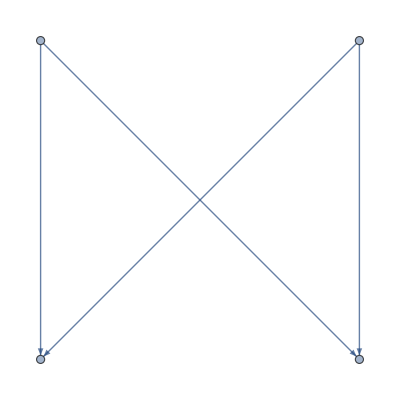

```mathematica
Graph[{"Ann"->"Bob","Ann"->"Barb","Abe"->"Bob","Abe"->"Barb"}]
```

To make this more informative, we need to provide some options. In particular, we want to see the names of the people associated with each vertex. To do this, we use the option VertexLabels with value “Name”.

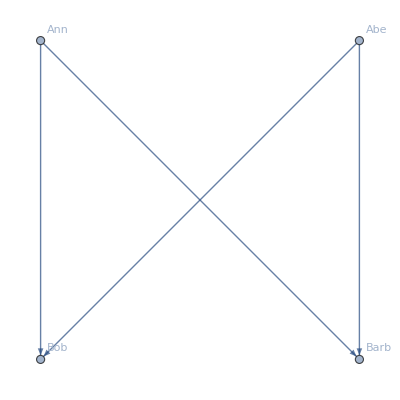

```mathematica
Graph[{"Ann"->"Bob","Ann"->"Barb","Abe"->"Bob","Abe"->"Barb"},VertexLabels->"Name"]
```

Listing the name of each vertex to the side like that can be difficult to read. So instead, we will increase the size of each vertex with the VertexSize option and use the Placed wrapper to put the name of each vertex in its center.

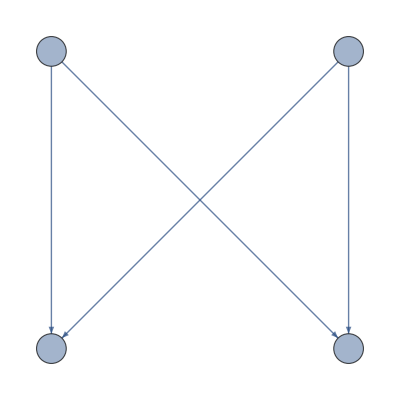

```mathematica
Graph[{"Ann"->"Bob","Ann"->"Barb","Abe"->"Bob","Abe"->"Barb"},VertexSize->Small,VertexLabels->Placed["Name",Center]]
```

Possible value for VertexSize include Tiny, Small, Medium, and Large, or a number between 0 and 1. A number causes the diameter of the vertices to be that proportion of the distance between the closest two vertices. More details about the use of VertexLabels and Placed will be given in Chapter 10.

Given an adjacency matrix, the function AdjacencyGraph will produce the Graph. The following draws a graph of the “divisible” relation using the div6M matrix. Note that the labels in this case are automatically chosen to be the integers from 1 to n, where n is the size of the matrix. An optional first argument can be provided to specify the vertex names.

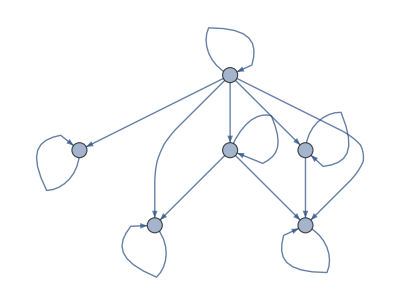

```mathematica
AdjacencyGraph[div6M,VertexSize->Medium,VertexLabels->Placed["Name",Center]]
```

Note that the reflexivity of the divisibility relation is apparent from the fact that all vertices have self-loops. When there are more than just a few vertices, this can become distracting. One way to remove the self-loops is by applying the SimpleGraph function. Note that this does not merely suppress the display of the loops; it actually deletes those edges from the graph.

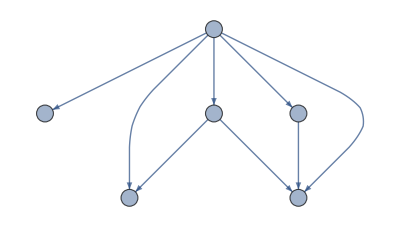

```mathematica
SimpleGraph[AdjacencyGraph[div6M],VertexSize->Medium,VertexLabels->Placed["Name",Center]]
```

A different approach, which preserves the edges internally while not displaying them, is to use the EdgeShapeFunction option. A full discussion of this option would be rather involved, but generally, EdgeShapeFunction allows you to define the function that controls how edges are drawn. Below, we use EdgeShapeFunction in combination with a pattern to suppress the drawing of self-loops.

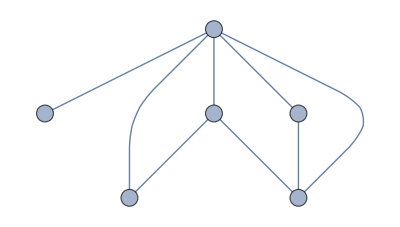

```mathematica
AdjacencyGraph[div6M,VertexSize->Medium,VertexLabels->Placed["Name",Center],EdgeShapeFunction->{x_->x_->None}]
```

In order to represent a relation satisfying relationQ as a graph, we will create a function drawRelation. At minimum, we need to transform the ordered pairs of the relation into rules. To do this, we can use the Apply function at level 1 as shown below.

```mathematica
Apply[Rule,div6,{1}]
```

{1→1,1→2,1→3,1→4,1→5,1→6,2→2,2→4,2→6,3→3,3→6,4→4,5→5,6→6}

Recall that @@@ is the operator form of the above expression.

```mathematica
Rule@@@div6
```

{1→1,1→2,1→3,1→4,1→5,1→6,2→2,2→4,2→6,3→3,3→6,4→4,5→5,6→6}

That is all that is necessary to graph the relation.

```mathematica
Graph[Rule@@@div6,VertexSize->Medium,VertexLabels->Placed["Name",Center]]
```

-Graphics-

Observe, however, that the graph is upside-down compared to the typical orientation. This is because the Wolfram Language has a preference for directed edges pointing downwards. To position the vertex 1 at the bottom, we reverse the direction of the edges. The Reverse function reverses the order of the elements. For example,

```mathematica
Reverse[{1,2,3}]
```

{3,2,1}

An optional second argument specifies the level, in order to reverse subexpressions.

```mathematica
Reverse[{{1,2},{3,4,5}},2]
```

{{2,1},{5,4,3}}

Thus, the desired graph representation of our divides relation is obtained as follows:

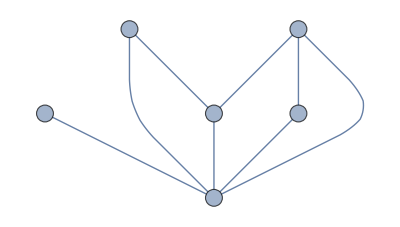

```mathematica
Graph[Apply[Rule,Reverse[div6,2],2],VertexSize->Medium,VertexLabels->Placed["Name",Center],EdgeShapeFunction->{x_->x_->None}]
```

The example above shows us how to define drawRelation.

```mathematica
drawRelation[R_?relationQ,size_:Medium]:=Graph[Apply[Rule,Reverse[R,2],2],VertexSize->size,VertexLabels->Placed["Name",Center],EdgeShapeFunction->{x_->x_->None}]
```

Note that we define the function with two arguments: the relation and a size argument. The colon after the Blank (_) specifies the default value. If the function is called with only one argument, the symbol Medium is used as the value of size. But if we need to make the vertices larger or smaller, we can choose a different value in the function call.

```mathematica
drawRelation[div6]
```

-Graphics-

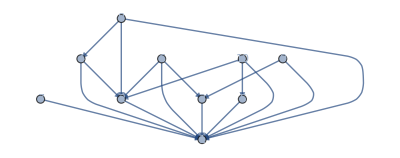

```mathematica
drawRelation[dividesRelation[10]]
```

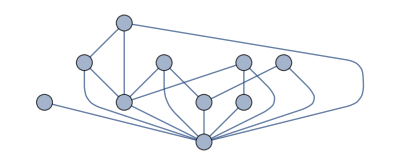

```mathematica
drawRelation[dividesRelation[10],Large]
```

### The Graph Object

In addition to being able to draw graphs, as described above, the Wolfram Language treats a Graph as an object that can be computed with.

To create a graph as an object, you use the Graph function, which is also the head of the object. Just as with GraphPlot and LayeredGraphPlot, you can use a list of rules indicating the edges as the input to Graph. For example, the following defines a Graph object representing the div6 relation.

```mathematica
div6G=drawRelation[div6]
```

-Graphics-

Observe that the output is a plot of the graph. However, div6G stores a Graph object, not an image.

```mathematica
FullForm[div6G]
```

Graph[List[1,2,3,4,5,6],List[DirectedEdge[1,1],DirectedEdge[2,1],DirectedEdge[3,1],DirectedEdge[4,1],DirectedEdge[5,1],DirectedEdge[6,1],DirectedEdge[2,2],DirectedEdge[4,2],DirectedEdge[6,2],DirectedEdge[3,3],DirectedEdge[6,3],DirectedEdge[4,4],DirectedEdge[5,5],DirectedEdge[6,6]],List[Rule[EdgeShapeFunction,List[Rule[DirectedEdge[4,4],None],Rule[DirectedEdge[1,1],None],Rule[DirectedEdge[2,2],None],Rule[DirectedEdge[6,6],None],Rule[DirectedEdge[5,5],None],Rule[DirectedEdge[3,3],None]]],Rule[VertexLabels,List[Placed["Name",Center]]],Rule[VertexSize,List[Medium]]]]

The main benefit of the Graph object is that the Wolfram Language can accept a Graph as an argument to many functions. For example, we can use this representation to determine whether or not the relation is transitive. To do this, we use the Wolfram Language’s implementation of the Floyd-Warshall all-pairs shortest path algorithm called GraphDistanceMatrix. This function returns a matrix whose (i,j) entry represents the shortest path from vertex i to vertex j. For example, the distance matrix for the div6 relation is:

```mathematica
GraphDistanceMatrix[div6G]//MatrixForm
```

(0 | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞
1 | ∞ | 0 | ∞ | ∞ | ∞
1 | 1 | ∞ | 0 | ∞ | ∞
1 | ∞ | ∞ | ∞ | 0 | ∞
1 | 1 | 1 | ∞ | ∞ | 0)

In a graph of a transitive relation, the distance between any two distinct elements must be either 1 or infinite (meaning there is no path between them). To see this, assume that you have a transitive relation and suppose there are elements A and Z that the all-pairs algorithm has determined have distance 3. That means there must be two elements, say M and N, such that A is connected to M is connected to N is connected to Z. From the point of view of the relation, then, (A,M) and (M,N) and (N,Z) are all members of the relation. However, if the relation is transitive, the fact that (A,M) and (M,N) are in the relation means that (A,N) is in the relation. In this case, A to N to Z is a shorter path (of length 2). Applying transitivity again shows that A and Z would be adjacent. While this does not amount to a proof, it should be convincing that we can check for transitivity by making sure that no two vertices in the graph of a relation have distance which is finite and greater than 1.

Here is the function.

```mathematica
transitiveGraphQ[g_Graph]:=Module[{d,i,j},
d=GraphDistanceMatrix[g];
Cases[Flatten[d],Except[0|1|Infinity]]=={}
]
```

After computing the distance matrix, the function uses Cases to identify any elements of the matrix that are not 0, 1, or ∞. Cases takes a list as the first argument, for which we Flatten the distance matrix, and a pattern as the second argument. In this case, we apply Except to 0, 1, and Infinity, separated by the Alternatives (|) operator. This means that anything other than those three symbols will match the pattern. The result of Cases will be the list of all the elements of the matrix that are other than 0, 1, and Infinity. Consequently, the relation is transitive if and only if that output is equal to the empty list.

```mathematica
transitiveGraphQ[div6G]
```

True

In this section, we have barely scratched the surface of graphs in the Wolfram Language. We will return to them in much greater detail in Chapter 10.

## 9.4 Closures of Relations

In this section, we develop algorithms to compute the reflexive, symmetric, and transitive closures of binary relations. We begin with the reflexive closure.

### Reflexive Closure

The algorithm for computing the reflexive closure of a relation, with the matrix representation, is very simple. We simply set each diagonal entry equal to 1. The resulting matrix represents the reflexive closure of the relation.

Note that this function will accept a matrix as input and return a modified version of that matrix. Internally, the function will need to work with a copy of the argument. That is, we will need to declare a local variable and set it equal to the argument. The reason for this is that when you execute a function in Mathematica, the argument is immediately substituted for the symbol used to represent it everywhere it appears. Thus, if x is the argument to a function and you call the function with a value of 3, an assignment such as x=5 will be interpreted as the illegal assignment 3=5.

Here is the function for computing the reflexive closure on a matrix representation.

```mathematica
reflexiveClosure[m_?matrix01Q]:=Module[{ans=m,i},
Do[ans[[i,i]]=1,{i,Dimensions[m][[1]]}];
ans
]
```

(Note that all the closure operations only apply to a relation on a set and are generally not valid for a relation from one set to a different set. This means we may assume that the matrix representation of the relation is square, which is imposed by matrix01Q.)

We use this function to find the reflexive closure of the example relation we introduced earlier in the chapter.

```mathematica
reflexiveClosure[exampleMatrix]//MatrixForm
```

(1 | 1 | 0 | 0
0 | 1 | 1 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1)

Recall that exampleMatrix represented the “is one less than” relation. Looking at the matrix above, you can see that the reflexive closure includes equality.

### Symmetric Closure

Next, we write a function for constructing the symmetric closure of a relation R. We use the observation that if (a,b) is a member of R then (b,a) must be included in the symmetric closure, so we can simply add it to the relation.

```mathematica
symmetricClosure[m_?matrix01Q]:=Module[{ans=m,i,j},
Do[If[ans[[i,j]]==1,ans[[j,i]]=1]
,{i,Dimensions[m][[1]]},{j,Dimensions[m][[2]]}];
ans
]
```

Applying this to our exampleMatrix yields the “different by 1” relation, and applying it to the “is a divisor of” relation yields the “is a divisor or multiple of” relation.

```mathematica
symmetricClosure[exampleMatrix]//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
symmetricClosure[div6M]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0 | 1)

### Transitive Closure

Having created functions to compute the reflexive and symmetric closures, we turn to implementing a function in the Wolfram Language to find the transitive closure of a relation. This is a more difficult problem than the earlier cases, both in terms of computational complexity and implementation. In the text, there are two algorithms outlined (a generic transitive closure and Warshall’s algorithm) and both will be covered in this section.

#### A Transitive Closure Function

First, we will implement the transitive closure algorithm presented as Algorithm 1 in Section 9.4 of the textbook. This will require the Boolean join and Boolean product operations on zero–one matrices that were introduced in Chapter 2. Recall from Section 2.6 of this manual that the BitAnd and BitOr functions correspond to the Boolean operations ∧ and ∨. Here are some examples.

```mathematica
BitAnd[1,1]
```

1

```mathematica
BitAnd[1,0]
```

0

```mathematica
BitOr[0,1]
```

1

```mathematica
BitOr[1,1]
```

1

Recall that for zero–one matrices A and B of the same size, the Boolean join of A and B is the matrix A∨B whose (i,j) entry is A_(i j)∨B_(i j). Since BitOr automatically threads over lists, it serves the role of the matrix join function without any additional work. For example,

```mathematica
joinA={{1,0},{0,1}};
joinA//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
joinB={{1,1},{0,0}};
joinB//MatrixForm
```

(1 | 1
0 | 0)

```mathematica
BitOr[joinA,joinB]//MatrixForm
```

(1 | 1
0 | 1)

Next, recall that for appropriately sized zero–one matrices, the Boolean product A⊙B is the matrix whose (i,j) entry is obtained by the formula

∨_(k=1)^n(a_(i k)∧b_(k j))

where n is the number of columns of A, which is also the number of rows of B. This is implemented in the boolProduct function. Refer to Section 2.6 where we first developed this function.

```mathematica
boolProduct::dimMismatch="The dimensions of the input matrices do not match.";
```

```mathematica
boolProduct[A_?matrix01Q,B_?matrix01Q]:=
Module[{m,kA,kB,n,output,i,j,c,p},
{m,kA}=Dimensions[A];
{kB,n}=Dimensions[B];
If[kA≠kB,Message[boolProduct::dimmismatch];Return[]];
output=ConstantArray[0,{m,n}];
For[i=1,i≤m,i++,
For[j=1,j≤n,j++,
c=BitAnd[A[[i,1]],B[[1,j]]];
For[p=2,p≤kA,p++,
c=BitOr[c,BitAnd[A[[i,p]],B[[p,j]]]];
];
output[[i,j]]=c;
]
];
output
]
```

As an example,

```mathematica
productA={{1,0,1},{0,1,0},{1,0,1}};
productA//MatrixForm
```

(1 | 0 | 1
0 | 1 | 0
1 | 0 | 1)

```mathematica
productB={{1,1,0},{0,1,0},{0,0,1}};
productB//MatrixForm
```

(1 | 1 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
boolProduct[productA,productB]//MatrixForm
```

(1 | 1 | 1
0 | 1 | 0
1 | 1 | 1)

We are now ready to implement Algorithm 1 from Section 9.4 for calculating the transitive closure. Recall that the idea of this algorithm is that we compute Boolean powers of the matrix of the relation, up to the size of the domain. At each step, we use the Boolean join on A=M^[i] and the result matrix B.

```mathematica
transitiveClosure[m_?matrix01Q]:=Module[{i,a=m,b=m},
Do[a=boolProduct[a,m];
b=BitOr[b,a]
,{i,2,Dimensions[m][[1]]}];
b
]
```

We test our transitive closure function on Example 7 from Section 9.4, where it was found that the relation with matrix representation

M_R=(1 | 0 | 1
0 | 1 | 0
1 | 1 | 0)

has transitive closure

M_(R^*)=(1 | 1 | 1
0 | 1 | 0
1 | 1 | 1)

```mathematica
example7={{1,0,1},{0,1,0},{1,1,0}};
example7//MatrixForm
```

(1 | 0 | 1
0 | 1 | 0
1 | 1 | 0)

```mathematica
transitiveClosure[example7]//MatrixForm
```

(1 | 1 | 1
0 | 1 | 0
1 | 1 | 1)

#### Warshall’s Algorithm

Next, we consider Warshall’s algorithm, presented as Algorithm 2 in Section 9.4. This algorithm is straightforward to implement.

```mathematica
warshall[m_?matrix01Q]:=Module[{i,j,k,w=m,n},
n=Dimensions[m][[1]];
For[k=1,k≤n,k++,
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
w[[i,j]]=BitOr[w[[i,j]],BitAnd[w[[i,k]],w[[k,j]]]]
]
]
];
w
]
```

Applying this to the same example as before, we see that the result is correct.

```mathematica
warshall[example7]//MatrixForm
```

(1 | 1 | 1
0 | 1 | 0
1 | 1 | 1)

We can compare these two functions in terms of execution time using the Wolfram Language Timing function. However, we must point out that this comparison for a single example does not prove anything about the complexity or relative performance of the two algorithms. Rather, it serves as a demonstration that, even for relations on small domains, the difference in the computational complexity of the algorithms is noticeable. We shall consider the following zero–one matrix that represents a relation on the set {1,2,3,4,5,6}.

```mathematica
transitiveCompare={{0,0,0,0,0,1},{1,0,1,0,0,0},{1,0,0,1,0,0},{1,0,0,0,1,0},{1,0,0,0,0,1},{0,1,0,0,0,0}};
transitiveCompare//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0)

```mathematica
Timing[warshall[transitiveCompare]]
```

{0.000837,{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}}}

```mathematica
Timing[transitiveClosure[transitiveCompare]]
```

{0.003448,{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}}}

From this example, we can see that Warshall’s algorithm can be a substantial improvement over the alternative, at least on this specific example. The reader is encouraged to explore this further. The reader may also wish to explore the Wolfram Language function TransitiveClosureGraph, which implements the Warshall algorithm and two other algorithms for finding transitive closures.

## 9.5 Equivalence Relations

In this section, we will examine how we can use Mathematica to compute with equivalence relations. There are three specific problems that we will address here: given an equivalence relation on a set, how to compute the equivalence class of an element; how to determine the number of equivalence relations on a finite set; and how to compute the smallest equivalence relation that contains a given relation on a finite set. Note that in this section, relations are assumed to be represented as in the start of this chapter, as lists of pairs satisfying relationQ.

First, we provide a test that determines whether or not a relation is an equivalence relation. Using the work that we have already done and recalling that an equivalence relation is simply a relation that is reflexive, symmetric, and transitive, this task is a simple one.

```mathematica
equivalenceQ[R_?relationQ]:=reflexiveQ[R]&&symmetricQ[R]&&transitiveQ[R]
```

As an example, define the equivalence relation “congruent mod 4” on the integers from 0 to n.

```mathematica
makeMod4[n_Integer]:=Module[{i,j},
Reap[
Do[If[Mod[i-j,4]==0,Sow[{i,j}]]
,{i,0,n},{j,0,n}]
][[2,1]]
]
```

```mathematica
mod4to8=makeMod4[8]
```

{{0,0},{0,4},{0,8},{1,1},{1,5},{2,2},{2,6},{3,3},{3,7},{4,0},{4,4},{4,8},{5,1},{5,5},{6,2},{6,6},{7,3},{7,7},{8,0},{8,4},{8,8}}

```mathematica
equivalenceQ[mod4to8]
```

True

### Equivalence Classes

Recall that, given an equivalence relation R and a member a of the domain of R, the equivalence class of a is the set of all members b of the domain for which the pair (a,b) belongs to R. In other words, it is the set of all elements in the domain that are R-equivalent to a. Therefore, the algorithm that determines the equivalence class of a particular element of the domain is fairly simple. We just search through R looking for all pairs of the form (a,b), adding each such second element b to the class. We do not have to search for pairs of the form (b,a) because equivalence relations are symmetric.

We can use the Cases function to implement this approach. Previously, we have used Select as a way to compute a sublist based on a criteria. Cases is similar, with two important differences. First, where Select uses a function to decide which elements of the original list to include, Cases uses a pattern. For example, to find all of the elements of mod4to8 with first element 3, we would need to match the pattern {3,_}, as shown below.

```mathematica
Cases[mod4to8,{3,_}]
```

{{3,3},{3,7}}

The second difference is that Cases can not only list those elements of the original list that match the pattern, but it can use a rule so that the output involves a modified version of the elements that match the pattern. For example, in order to return only the second elements of each pair (referring to the output above, the 3 and 7), we enter the following.

```mathematica
Cases[mod4to8,{3,b_}->b]
```

{3,7}

The following function returns the equivalence class for a given equivalence relation and a point in the domain. We use Cases as illustrated above and apply Union to be certain that there are no duplicates in the output and to order the result.

```mathematica
equivalenceClass[R_?equivalenceQ,a_]:=Module[{b},
Union[Cases[R,{a,b_}->b]]
]
```

As an example, we compute the equivalence class of 3 in the modulo 4 relation on the domain {1,2,…,30}.

```mathematica
equivalenceClass[makeMod4[30],3]
```

{3,7,11,15,19,23,27}

### Number of Equivalence Relations on a Set

Next, we consider how to construct all of the equivalence relations on a given (finite) set. The straightforward way to do this is to construct all relations on the given domain and then check them to see if they are equivalence relations. Since a relation on a set A is merely a subset of A×A, generating all relations is the same as generating all subsets of A×A.

To implement this, we begin by creating the set A×A using the Wolfram Language Tuples function. Tuples will take a list and a positive integer (e.g., 2) and return the list of all possible tuples of the specified length. In effect, Tuples[A,2] produces A×A. For example, to compute {1,2}×{1,2}, we would enter the following:

```mathematica
Tuples[{1,2},2]
```

{{1,1},{1,2},{2,1},{2,2}}

We apply the Subsets function to A×A in order to find all subsets. Given a list, Subsets produces the list of all sublists. For example, applying Subsets to the output from Tuples above produces the following.

```mathematica
Subsets[Tuples[{1,2},2]]
```

{{},{{1,1}},{{1,2}},{{2,1}},{{2,2}},{{1,1},{1,2}},{{1,1},{2,1}},{{1,1},{2,2}},{{1,2},{2,1}},{{1,2},{2,2}},{{2,1},{2,2}},{{1,1},{1,2},{2,1}},{{1,1},{1,2},{2,2}},{{1,1},{2,1},{2,2}},{{1,2},{2,1},{2,2}},{{1,1},{1,2},{2,1},{2,2}}}

The Column function will place each element of the output from Subsets on a separate line, so as to make it easier to read. As is our habit for functions that modify the display of output, we apply Column in the postfix form.

```mathematica
Subsets[Tuples[{1,2},2]]//Column
```

{}
{{1,1}}
{{1,2}}
{{2,1}}
{{2,2}}
{{1,1},{1,2}}
{{1,1},{2,1}}
{{1,1},{2,2}}
{{1,2},{2,1}}
{{1,2},{2,2}}
{{2,1},{2,2}}
{{1,1},{1,2},{2,1}}
{{1,1},{1,2},{2,2}}
{{1,1},{2,1},{2,2}}
{{1,2},{2,1},{2,2}}
{{1,1},{1,2},{2,1},{2,2}}

To complete the process, we need to limit the output to those subsets of A×A which are equivalence relations. For this, we will apply Select. Recall that Select applied to a list and a function will produce the sublist of the original for which the function returns True. In this case, the function we use will be equivalenceQ.

```mathematica
Select[Subsets[Tuples[{1,2},2]],equivalenceQ]//Column
```

{}
{{1,1}}
{{2,2}}
{{1,1},{2,2}}
{{1,1},{1,2},{2,1},{2,2}}

This example shows us how to build a more general function. allEquivalenceRelations below will accept a list as its argument and will output all of the equivalence relations.

```mathematica
allEquivalenceRelations[A_List]:=Select[Subsets[Tuples[A,2]],equivalenceQ]
```

For example, there are 15 equivalence relations on {1,2,3}.

```mathematica
Length[allEquivalenceRelations[{1,2,3}]]
```

15

### Closure

The last question to be considered in this section is the problem of finding the smallest equivalence relation containing a relation R.

The key idea is that we need to find the smallest relation containing R that is reflexive, symmetric, and transitive. Recalling the previous section on closures, it is natural to think that we may compute the reflexive closure, the symmetric closure, and then the transitive closure, one after the other. The only concern would be that one closure would no longer have one of the previous properties. The argument below explains why applying this sequence of closure operations does in fact yield an equivalence relation; however, contrast this with Exercise 36 of Section 9.4 of the textbook.

Create the reflexive closure of R, call it P.

Compute the symmetric closure of P and call this Q. Note that Q is still reflexive since no pairs were removed from the relation and no elements were added to the domain. Thus, Q is both symmetric and reflexive.

Compute the transitive closure of Q and name this S. Note that S is still reflexive for the same reason as above. Moreover, S is still symmetric since, if (a,b) and (b,c) are in Q to force the addition of (a,c), then since Q is symmetric, (c,b) and (b,a) must also be in Q forcing (c,a) to also be included in S. Hence, S is an equivalence relation.

We implement this method as the composition of the four methods relationToMatrix, reflexiveClosure, symmetricClosure, and then transitiveClosure.

```mathematica
equivalenceClosure[R_?relationQ]:=transitiveClosure[symmetricClosure[reflexiveClosure[relationToMatrix[R]]]]
```

As an example, recall the div6 relation representing the “is a divisor of” relation on {1,2,3,4,5,6}. We can see that the smallest equivalence relation that contains div6 is the relation in which every number is related to every other number.

```mathematica
equivalenceClosure[div6]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1)

This is unsurprising, since 1 is a divisor of every number meaning that, in any equivalence relation containing the “divides” relation, 1 is related to every number. We can make this example slightly more interesting by removing 1.

```mathematica
div17minus1=dividesRelation[Range[2,17]]
```

{{2,2},{2,4},{2,6},{2,8},{2,10},{2,12},{2,14},{2,16},{3,3},{3,6},{3,9},{3,12},{3,15},{4,4},{4,8},{4,12},{4,16},{5,5},{5,10},{5,15},{6,6},{6,12},{7,7},{7,14},{8,8},{8,16},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17}}

```mathematica
equivalenceClosure[div17minus1]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(Note the first row and column still correspond to 1 because of the way the matrix is constructed in relationToMatrix.) In this example, you see that 11, 13, and 17 become isolated, being the three primes in the set which do not have multiples of them also included.

## 9.6 Partial Orderings

In this section, we consider partial orderings (also called partial orders) and related topics, including maximal and minimal elements, Hasse diagrams, and lattices.

### Partial Orders and Examples

First, we will define a new predicate in the Wolfram Language for partial orders and create some examples of them.

Recall that a partial order is a binary relation on a set that satisfies the three conditions of being reflexive, antisymmetric, and transitive. We define the predicate to be a function that tests an object against the definition of a partial order. It is very similar to the equivalenceQ function we created in the previous section.

```mathematica
partialOrderQ[R_?relationQ]:=reflexiveQ[R]&&antisymmetricQ[R]&&transitiveQ[R]
```

Now, we can use the partialOrderQ function to determine whether a list is a partial order. For example, we can check that the div6 relation we defined earlier (recall that this is the “divides” relation on the set 1 through 6) is a partial order.

```mathematica
partialOrderQ[div6]
```

True

We create some additional examples of partial orderings that we can use in the remainder of the section. The div17minus1 relation (this is the “divides” relation on the set 2 through 17 defined in the previous section) is a partial order.

```mathematica
partialOrderQ[div17minus1]
```

True

Indeed, all the relations created via the dividesRelation function will be partial orders.

Next, we create a function to produce examples of a class of lattices (we will discuss lattices more below, for now it is enough that these examples are partial orders). The divisorLattice function will create the partial order whose domain is the set of positive divisors of a given number and whose order is defined by the “divides” relation. We only need to apply the dividesRelation function to the divisors of the given number.

```mathematica
divisorLattice[n_Integer]:=dividesRelation[Divisors[n]]
```

The Divisors function produces the list of positive divisors of the given integer.

```mathematica
divisorLattice[10]
```

{{1,1},{1,2},{1,5},{1,10},{2,2},{2,10},{5,5},{5,10},{10,10}}

```mathematica
partialOrderQ[divisorLattice[10]]
```

True

Finally, for a bit of variety, we create the posets whose Hasse diagrams are shown in Figure 8(a) and Figure 10 in Section 9.6.

```mathematica
fig8A={{"a","a"},{"a","b"},{"a","c"},{"a","d"},{"a","e"},{"a","f"},{"b","b"},{"b","c"},{"b","d"},{"b","e"},{"b","f"},{"c","c"},{"c","e"},{"c","f"},{"d","d"},{"d","e"},{"d","f"},{"e","e"},{"e","f"},{"f","f"}};
```

```mathematica
partialOrderQ[fig8A]
```

True

```mathematica
fig10={{"A","A"},{"A","B"},{"A","D"},{"A","F"},{"A","G"},{"B","B"},{"B","D"},{"B","F"},{"B","G"},{"C","C"},{"C","B"},{"C","D"},{"C","F"},{"C","G"},{"D","D"},{"D","G"},{"E","E"},{"E","F"},{"E","G"},{"F","F"},{"F","G"},{"G","G"}};
```

```mathematica
partialOrderQ[fig10]
```

True

### Hasse Diagrams

Now that we have defined a predicate and have examples at our disposal, we turn to the problem of using Mathematica to draw Hasse diagrams of partial orders. As illustrated in the textbook, a Hasse diagram is a very useful tool for visualizing and understanding posets. Drawing the Hasse diagram for a poset is not as simple as drawing all of the elements of the set and then connecting all related pairs with an edge. Doing so would create an extremely messy, and not very useful, diagram. Instead, a Hasse diagram contains only those edges that are absolutely necessary to reveal the structure of the poset.

The Wolfram Language includes the function TransitiveReductionGraph, which can be used to create a Hasse diagram from the Graph representing a relation. For example, if we begin with the relation described by Figure 10 from the textbook and use Apply at level 1 (@@@) to transform each pair in the relation to a Rule, we have the needed data to construct a Graph.

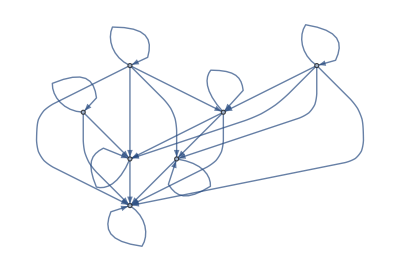

```mathematica
Graph[Rule@@@fig10]
```

As discussed in Section 9.3 of this manual, the Wolfram Language defaults to drawing arrows pointed downward. We use Reverse in combination with Map (/@) in order to reverse the direction of the edges.

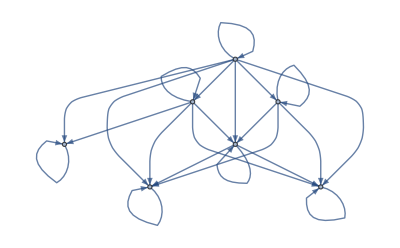

```mathematica
fig10Graph=Graph[Rule@@@Reverse/@fig10]
```

Applying TransitiveReductionGraph, we can see that the result is, except for some slight repositioning of the vertices, the same graph shown in Figure 10. Refer back to Section 9.3 of this manual for the use of VertexSize and VertexLabels.

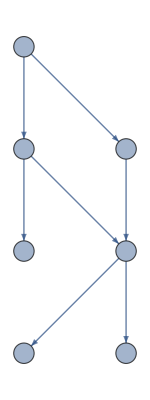

```mathematica
TransitiveReductionGraph[fig10Graph,VertexSize->Medium,VertexLabels->Placed["Name",Center]]
```

While the Wolfram Language contains this useful function, we will develop our own functions for producing Hasse diagrams in order to better understand the connection between the partial order as a set of ordered pairs and the diagram.

#### Covering Relations

The covering relation for a partial order is a minimal representation of the partial order, from which the partial order can be reconstructed via transitive and reflexive closure.

Let ≼ be a partial order on a set S. Recall that an element y in S covers an element x in S if x≺y, x≠y, and there is no element z of S, different from x and y, such that x≺z≺y. In other words, y covers x if y is greater than x and there is no intermediary element. The set of pairs (x,y) for which y covers x is the covering relation of ≼.

As a simple example, consider the set {1,2,3,4} ordered by magnitude, that is, the usual “less than or equal to” relation. This relation consists of 10 ordered pairs:

{(1,1),(1,2),(1,3),(1,4),(2,2),(2,3),(2,4),(3,3),(3,4),(4,4)}

Its covering relation is the set

{(1,2),(2,3),(3,4)}

which consists of only three pairs. All the other pairs of the partial order can be inferred from the covering relation using transitivity and reflexivity. For instance, (1,3) can be recovered from (1,2) and (2,3) via transitivity. Note that the covering relation involves many fewer pairs and thus is a much more efficient way to represent the partial order, at least in terms of storage.

Our goal is to write a function in the Wolfram Language to draw the Hasse diagram of a given partial order. Since a Hasse diagram is, in fact, the graph of the associated covering relation, most of the work will be done in a function to find the covering relation of the partial order.

First, we need a test to check whether a given element covers another.

```mathematica
coversQ[R_?partialOrderQ,{x_,y_}]:=Module[{z,checkSet},
Catch[
If[x==y,Throw[False]];
If[!MemberQ[R,{x,y}],Throw[False]];
checkSet=Complement[findDomain[R],{x,y}];
Do[If[MemberQ[R,{x,z}]&&MemberQ[R,{z,y}],Throw[False]]
,{z,checkSet}];
Throw[True]
]
]
```

This function works by first checking to see if the two elements x and y are equal to each other or if the pair (x,y) fails to be in the partial order. In either of these situations, y does not cover x. Assuming the pair of elements passes these basic hurdles, the function then checks every other element of the domain. If it can find an element that sits between x and y, then we know they do not cover. If no element sits between them, then in fact y does cover x.

We can now construct the covering relation of a partial order. The function below simply checks every element of the given relation to see if one covers the other and includes only those that do in the output relation. It uses Select to execute the check over each element of the given relation and eliminate those that do not belong. The test used is a pure Function (&) formed from coversQ.

```mathematica
coveringRelation[R_?partialOrderQ]:=Select[R,coversQ[R,#]&]
```

We consider two examples. First, the example described above, of the set {1,2,3,4} ordered by magnitude.

```mathematica
coveringRelation[{{1,1},{1,2},{1,3},{1,4},{2,2},{2,3},{2,4},{3,3},{3,4},{4,4}}]
```

{{1,2},{2,3},{3,4}}

Second, we find the covering relation of a lattice.

```mathematica
coveringRelation[divisorLattice[30]]
```

{{1,2},{1,3},{1,5},{2,6},{2,10},{3,6},{3,15},{5,10},{5,15},{6,30},{10,30},{15,30}}

#### Drawing Hasse Diagrams

Now, we will use the covering relation in order to write a function to draw the Hasse diagram for partial orders. By using the coveringRelation function that we just completed, we can create the graph associated to a partial order.

As above, we use Map (/@) to Reverse the order of the pairs and then Apply at level 1 (@@@) to transform the pairs of the relation into lists.

As in Section 9.3 of this manual, we include an optional argument to control the size of vertices, with default value Medium.

```mathematica
hasseDiagram[R_?partialOrderQ,size_:Medium]:=Module[{edges},
edges=Rule@@@Reverse/@coveringRelation[R];
Graph[edges,VertexSize->size,VertexLabels->Placed["Name",Center]]
]
```

As an example, here is a diagram representing the divisor lattice of 210.

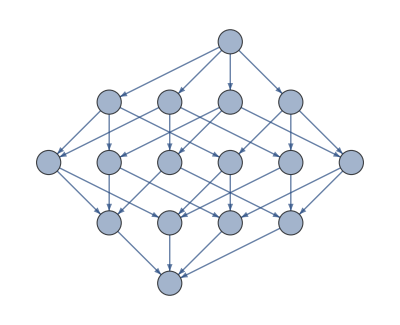

```mathematica
hasseDiagram[divisorLattice[2*3*5*7],Large]
```

Here are the Hasse diagrams for some of the other examples we discussed in this section.

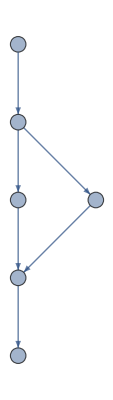

```mathematica
hasseDiagram[fig8A]
```

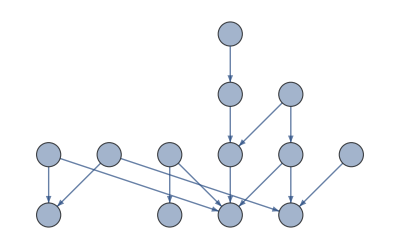

```mathematica
hasseDiagram[div17minus1,Large]
```

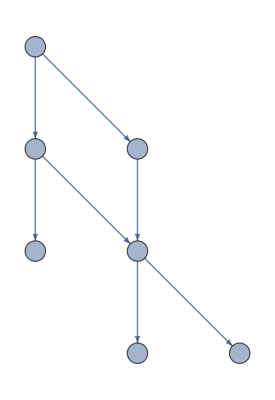

```mathematica
hasseDiagram[fig10]
```

Comparing this last example to the diagram given in the textbook illustrates that, while using the LayeredGraphPlot function does not result in quite as appealing graphs as those that are created by hand, it still provides a fairly useful graph. Also note that you can tweak the results of LayeredGraphPlot dynamically. To adjust the location of a vertex, place the mouse pointer over the vertex, double-click to enter editing mode for the graph, and double-click again to edit the vertex. You can then click and drag the vertex to specify a different position.

### Maximal and Minimal Elements

We will construct a function that determines the set of minimal elements of a partially ordered set.

The function takes two arguments: a partial order R and a subset S of the domain of R. It returns the set of minimal elements of S with respect to R. It first initializes the set of minimal elements to all of S and then removes those that are not minimal.

```mathematica
minimalElements[R_?partialOrderQ,S_List]:=Module[{M,s,t},
M=S;
Do[
Do[
If[MemberQ[R,{t,s}],M=Complement[M,{s}]]
,{t,Complement[S,{s}]}]
,{s,S}];
M
]
```

We can see this work on our div6 partial order. As we will be using the div6 partial order for many examples in this section, its Hasse diagram may also be useful.

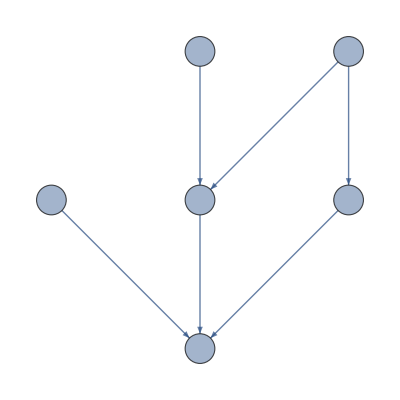

```mathematica
hasseDiagram[div6]
```

```mathematica
minimalElements[div6,Range[6]]
```

{1}

```mathematica
minimalElements[div6,Range[2,6]]
```

{2,3,5}

Note that, by reversing the relation and thus the order, we can compute maximal elements very easily.

```mathematica
maximalElements[R_?partialOrderQ,S_List]:=minimalElements[inverseRelation[R],S]
```

```mathematica
maximalElements[div6,Range[6]]
```

{4,5,6}

### Least Upper Bound

Next, we will write a function for computing the least upper bound of a set with respect to a partial order, if it exists. Our function will return the value Null in the case that the set has no least upper bound.

First, we create a function upperBoundQ that determines whether a given element is an upper bound of a set with respect to a relation. It accomplishes this by checking to make sure that the given element is greater than every element of the set.

```mathematica
upperBoundQ[R_?partialOrderQ,S_List,u_]:=Module[{s},
Catch[
Do[If[!MemberQ[R,{s,u}],Throw[False]]
,{s,S}];
Throw[True]
]
]
```

For example, under the div6 relation, 6 is an upper bound of {1,2,3}, but not of {1,2,3,4}.

```mathematica
upperBoundQ[div6,{1,2,3},6]
```

True

```mathematica
upperBoundQ[div6,{1,2,3,4},6]
```

False

Second, we write a function to find all of the upper bounds for a given set. We do this by considering every element of the domain of the relation and checking to see which are upper bounds, using the upperBoundQ function.

```mathematica
upperBounds[R_?partialOrderQ,S_List]:=Module[{domR,d,U={}},
domR=findDomain[R];
Do[If[upperBoundQ[R,S,d],AppendTo[U,d]]
,{d,domR}];
U
]
```

For instance, the upper bounds of the set {1,2} under div6 are:

```mathematica
upperBounds[div6,{1,2}]
```

{2,4,6}

To complete the task of finding the least upper bound of a set, we merely use upperBounds to compute all of the upper bounds for the set, use minimalElements to see which of the upper bounds are minimal, and then check to see how many minimal upper bounds are found. If there is exactly one minimal upper bound, then this is the least upper bound. Otherwise, the set has no least upper bound.

```mathematica
leastUpperBound[R_?partialOrderQ,S_List]:=Module[{U,M},
U=upperBounds[R,S];
M=minimalElements[R,U];
If[Length[M]≠1,Null,M[[1]]]
]
```

For example, the least upper bounds of {1,2} and {1,2,3} are found below, while {4,5} has no least upper bound in the domain of div6 and so does not return a value.

```mathematica
leastUpperBound[div6,{1,2}]
```

2

```mathematica
leastUpperBound[div6,{1,2,3}]
```

6

```mathematica
leastUpperBound[div6,{4,5}]
```

### Lattices

As the last topic in this section, we will consider the problem of determining whether a partial order is a lattice. The approach we will take is a good example of top–down programming. The test we design here will confirm that the function divisorLattice written at the beginning of this section does indeed produce lattices.

Recall that a partial order is a lattice if every pair of elements has both a least upper bound and a greatest lower bound (in lattices, these are also referred to as the supremum and infimum of the pair or as their meet and join). With this in mind, we can write the following function (with the understanding that the helper functions still need to be written).

```mathematica
latticeQ[R_?partialOrderQ]:=hasLUBs[R]&&hasGLBs[R]
```

We need to write the two helper functions: hasLUBs to determine if the partial order satisfies the property that every pair of elements has a least upper bound, and hasGLBs to determine if every pair has a greatest lower bound. Just as we did above with the maximalElements function, we really only need to write one function if we recognize that a partial order satisfies the greatest lower bound property if the inverse relation satisfies the least upper bound property. So, we compose hasLUBs with the inverseRelation function to create hasGLBs.

```mathematica
hasGLBs[R_?partialOrderQ]:=hasLUBs[inverseRelation[R]]
```

We complete the work by coding the hasLUBs function. We must test whether, for a given relation R, each pair a and b in the domain of R has a least upper bound with respect to R.

```mathematica
hasLUBs[R_?partialOrderQ]:=Module[{domR,a,b},
domR=findDomain[R];
Catch[
Do[If[leastUpperBound[R,{a,b}]===Null,Throw[False]]
,{a,domR},{b,domR}];
Throw[True]
]
]
```

Finally, all of the subroutines that go into making up the latticeQ program are complete, and we can test it on some examples. Contrast the relations constructed by the dividesRelation function versus those made by divisorLattice.

```mathematica
latticeQ[dividesRelation[10]]
```

False

```mathematica
latticeQ[divisorLattice[20]]
```

True

## Solutions to Computer Projects and Computations and Explorations

### Computer Projects 15

Given a partial ordering on a finite set, find a total ordering compatible with it using topological sorting.

Solution: The textbook contains a detailed explanation of topological sorting and summarizes it as Algorithm 1 of Section 9.6.

The set S is initialized to the domain of the given relation. At each step, find a minimal element (using the minimalElements function we created above) of S. This minimal element is removed from S and added as the next largest element of the total ordering. This repeats until S is empty and consequently all elements are in the total order.

```mathematica
topologicalSort[R_?partialOrderQ]:=Module[{S,a,T},
T={};
S=findDomain[R];
While[S≠{},
a=minimalElements[R,S][[1]];
S=Complement[S,{a}];
T=AppendTo[T,a]
];
T
]
```

We apply this procedure to fig10.

```mathematica
topologicalSort[fig10]
```

{A,C,B,D,E,F,G}

### Computations and Explorations 1

Display all the different relations on a set with four elements.

Solution: As is often the case, the specific question can be solved as an instance of a more general problem. We provide a very simple function that will compute all relations on any finite set. This procedure merely constructs the Cartesian product C=S×S using Tuples and then makes use of the Subsets function to obtain all of the relations on the set.

```mathematica
allRelations[S_List]:=Subsets[Tuples[S,2]]
```

We now test our procedure on a set with 2 elements. (This keeps the output to a reasonable length.) We use Column to display each relation on its own line.

```mathematica
allRelations[{1,2}]//Column
```

{}
{{1,1}}
{{1,2}}
{{2,1}}
{{2,2}}
{{1,1},{1,2}}
{{1,1},{2,1}}
{{1,1},{2,2}}
{{1,2},{2,1}}
{{1,2},{2,2}}
{{2,1},{2,2}}
{{1,1},{1,2},{2,1}}
{{1,1},{1,2},{2,2}}
{{1,1},{2,1},{2,2}}
{{1,2},{2,1},{2,2}}
{{1,1},{1,2},{2,1},{2,2}}

The reader is encouraged to determine the running time and output length for the function when the input set has cardinality 4 or 5. Keep in mind that there are 2^(n^2) relations on a set with n members.

### Computations and Explorations 4

Determine how many transitive relations there are on a set with n elements for all positive integers n with n≤7.

Solution: We will construct each possible n×n zero–one matrix using an algorithm similar to binary counting. The approach is as follows:

For each number from 0 to 2^(n^2)-1, we create a list of 0s and 1s that is the base 2 representation of that integer. We can do this with the IntegerDigits function. The syntax IntegerDigits[i,2,n^2] returns a list whose entries are the base 2 representation of the integer i, padded with 0s if necessary to obtain a list of length n^2.

Then, create a matrix M whose entries are that list of values. These are all possible 2^(n^2) zero–one matrices (the reader is encouraged to prove this statement). We use the Partition function on the list with second argument n to split the list of n^2 values into a n×n matrix.

Finally, evaluate the transitive closure of each of those matrices, using the warshall function from Section 9.4 above. We test to see if the matrix is transitive by checking to see if it is equal to its transitive closure. If so, it is counted as a transitive relation.

The implementation is as follows:

```mathematica
countTransitive[n_Integer]:=Module[{i,j,T,M,count=0},
For[i=0,i≤2^(n^2)-1,i++,
T=IntegerDigits[i,2,n^2];
M=Partition[T,n];
If[warshall[M]==M,count++]
];
count
]
```

We use the function on a relatively small value and leave further computations to the reader.

```mathematica
countTransitive[3]
```

171

There are more efficient approaches than the one presented here. For example, we know that any relation between (in the subset sense) a relation and its transitive closure is not transitive. Using that fact suggests an algorithm in which each application of warshall can potentially eliminate intermediate relations from future consideration.

### Computations and Explorations 5

Find the transitive closure of a relation of your choice on a set with at least 20 elements. Either use a relation that corresponds to direct links in a particular transportation or communications network or use a randomly generated relation.

Solution: We will generate a random zero–one matrix with dimension 8×8, and then apply Warshall’s algorithm to compute the transitive closure. (We use a smaller size than specified in the problem so as to be able to display the result easily.)

To generate a random zero–one matrix, we use the RandomVariate function. This function was first discussed in Section 7.2. The first argument to RandomVariate must be a probability distribution. We will use the BernoulliDistribution, which randomly chooses 0 or 1, with parameter .1. This means that 1 is chosen with probability .1, resulting in a fairly sparse matrix. This increases the chance that the transitive closure will have entries that are not 1. The second argument to RandomVariate specifies the number of times to sample the distribution. By using a list, for example {8,8}, the function will output a matrix of that size.

```mathematica
randomMatrix=RandomVariate[BernoulliDistribution[.1],{8,8}];
randomMatrix//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
warshall[randomMatrix]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Exercises

The relationToMatrix function converts a relation satisfying relationQ to a zero–one matrix representation. Write a function to convert a zero–one matrix representation of a relation to a relationQ representation.

Write a function in the Wolfram Language with the signature

makeRelation[S:{__Integer},f_Function]

that creates the relation {(a,b)∈S×S:f(a,b) is true}. That is, makeRelation should return the set of all ordered pairs (a,b) of elements of S for which the pure Function (&) f evaluates to true when a and b are substituted for the Slots (#) in f. For example, your function should accept an expression such as

#1+#2<#1*#2&

Write a function in the Wolfram Language to generate a random relation on a given finite set of integers.

Use the function you wrote in the preceding exercise to investigate the probability that an arbitrary relation has each of the following properties: (a) reflexivity; (b) symmetry; (c) anti-symmetry; and (d) transitivity.

Write functions to determine whether a given relation is irreflexive or asymmetric. (See the text for definitions of these properties.)

Implement Tables 11 and 12 from Section 9.2 as Dataset objects. Then:

Find the projection of the Parts_inventory database onto the Part_number and Color_code fields.

Join the two databases across the Part_number and Project fields.

Select those entries for which the Quantity is less than 10.

Write functions to compute the count and support of an itemset. Then write a function to test whether an itemset is frequent relative to a given threshold; your function should accept the itemset, the set of transactions, and the threshold as arguments.

Investigate the Apriori algorithm (see Exercise 40 from Section 9.2 and Writing Project 3) and then implement this algorithm in the Wolfram Language.

Investigate the ratio of the size of an arbitrary relation to the size of its transitive closure. How much does the transitive closure make a relation "grow" on average?

Examine the function φ defined as follows. For a positive integer n, we define φ(n) to be the number of relations on a set of n elements whose transitive closure is the “all” relation. (If A is a set, then the “all” relation on A is the relation A×A with respect to which every member of A is related to every other member of A, including itself.)

Write a function in the Wolfram Language that finds the antichain with the greatest number of elements in a partial ordering. (See the text for the definition of antichain.)

The transitive reduction of a relation G is the smallest relation H such that the transitive closure of H is equal to the transitive closure of G. Use Mathematica to generate some random relations on a set with ten elements and find the transitive reduction of each of these random relations.

Write a function that computes a partial order, given its covering relation.

Write a function to determine whether a given lattice is a Boolean algebra, by checking whether it is distributive and complemented. (See the text for definitions.)